## Results from “Heterodyne v3.nb”

Δ_p → ∞, 
Gaussian filters [J. Rehacek, Y.S. Teo,and  S. Wallentowitz, Sci .Rep. (2015)]: 
δ_HOM=ϵ_HOM/2 := (1-η)/(2η),δ_HET=ϵ_HET/2:=(2-η)/(2η)

#### [Calc] Gaussian integrals

```mathematica
GaussianIntegral[M_]:=(2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(M⟦2,2⟧^2-4 M⟦1,3⟧ M⟦3,1⟧)) π)/(√(-4 M⟦1,3⟧+M⟦2,2⟧^2/M⟦3,1⟧) √(-M⟦3,1⟧));
ExpCoefficientsToMatrix[expr_,x_,p_]:=CoefficientList[Exponent[expr,ⅇ],{x,p},{3,3}];

TruncatedGaussInt[v_,Δ_]:=(ⅇ^(v⟦1⟧-v⟦2⟧^2/(4 v⟦3⟧)) √π (-Erfi[(v⟦2⟧-Δ v⟦3⟧)/(2 √v⟦3⟧)]+Erfi[(v⟦2⟧+Δ v⟦3⟧)/(2 √v⟦3⟧)]))/(2 √v⟦3⟧);(* Trunated Gaussian integrals ∫_(-Δ/2)^(Δ/2) ⅇ^(c x^2+b x +a)ⅆx*)
```

#### [Rslt] Essential code

```mathematica
ϵHOM[ηH_]:=2((1-ηH)/(2 ηH)); (* 2δ *)
ϵHET[ηH_]:=2((2-ηH)/(2 ηH)); (* 2δ *)

(* THRESHOLD *)
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

WnTHR[t_,α_,θ_,x1_,p1_,η_,s_]:=((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2]Wcat[t α,θ,x1,p1,-1]+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2]Wcat[t α,θ,x1,p1,1];
PsTHR[t_,α_,η_,s_]:=(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))])/(Exp[α^2]+s Exp[-α^2]);

(* HOMODYNE *)WunHOM[t_,r_,α_,θ_,x1_,p1_,Δx_,ϵ_,s_]:=1/(2 π (ⅇ^(2 α^2)+s))ⅇ^(-p1^2-x1^2) (ⅇ^(2 t^2 α^2) s Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])] (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])] (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]));
PsHOM[t_,r_,α_,θ_,Δx_,ϵ_,s_]:=1/(2 (ⅇ^(2 α^2)+s))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]));
WnHOM[t_,r_,α_,θ_,x1_,p1_,Δx_,ϵ_,s_]:=Re[WunHOM[t,r,α,θ,x1,p1,Δx,ϵ,s]/PsHOM[t,r,α,θ,Δx,ϵ,s]];

(* HETERODYNE *)
WunHET[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(4π(1+s ⅇ^(-2 α^2)))   ⅇ^(-p1^2-x1^2)(ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])](Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))])+ ⅇ^(2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])]s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));PsHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:= (ⅇ^(-2 α^2))/(4(1+s ⅇ^(-2 α^2)))(s (Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]));

WnHET[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=Re[WunHET[t,r,α,θ,x1,p1,Δx,Δp,ϵ,s]/PsHET[t,r,α,θ,Δx,Δp,ϵ,s]];


(* COMPARISONS of THRESHOLD with ... *)
ηPurity[t_,r_,α_,θ_,η_,s_]:=(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2);
FidelityTGTTHR[t_,r_,α_,η_,s_]:= (1+ⅇ^(4 (-1+r^2) α^2)+2 ⅇ^(2 (-1+r^2) α^2) s+2 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(2 r^2 α^2 (-1+η)) s^2+ⅇ^(2 α^2 (-2+r^2 (1+η))) s^2)/(2 (1+ⅇ^(2 (-1+r^2) α^2) s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s));
(* ... HOM *)
PsηRelativeImprovementHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=Re[(PsHOM[t,r,α,θ,Δx,ϵ,s]-PsTHR[t,α,η,s])/PsTHR[t,α,η,s]];
FidelityHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])));
FidelityGapHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=FidelityTGTTHR[t,r,α,η,s]-FidelityHOM[t,r,α,θ,Δx,ϵ,1,s];
ηRelativeOverlapHOM[t_,r_,α_,θ_,Δx_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-FidelityHOM[t,r,α,θ,Δx,ϵ,η,s];
ηFitHOM[t_,r_,α_,θ_,Δx_,ϵ_,s_]:=FindRoot[{Re[ηRelativeOverlapHOM[t,r,α,θ,Δx,ϵ,η,s]]==0},{η,1}];
ΔFitHOM[t_,r_,α_,θ_,ϵ_,η_,s_]:=FindRoot[{Re[ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵ,η,s]]==0},{Δ,1}];

(* ... HET *)
PsηRelativeImprovementHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=Re[(PsHET[t,r,α,θ,Δx,Δp,ϵ,s]-PsTHR[t,α,η,s])/PsTHR[t,α,η,s]];
FidelityHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])));
FidelityGapHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=FidelityTGTTHR[t,r,α,η,s]-FidelityHET[t,r,α,θ,Δx,Δp,ϵ,1,s];
ηRelativeOverlapHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,η,s]-FidelityHET[t,r,α,θ,Δx,Δp,ϵ,η,s];
ηFitHET[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:=FindRoot[{Re[ηRelativeOverlapHET[t,r,α,θ,Δx,Δp,ϵ,η,s]]==0},{η,1}];
ΔFitHET[t_,r_,α_,θ_,ϵ_,η_,s_]:=FindRoot[{Re[ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵ,η,s]]==0},{Δ,1}];

(* Numerically fnding the point where Threshold and dyne measurements are equivalent, i.e. where RO(η,Δ)==0 AND RI(η,Δ)==0 *)
EquivalencePointHOM[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];
EquivalencePointHET[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];

EquivalencePointTGTHOM[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{FidelityGapHOM[t,r,α,θ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];
EquivalencePointTGTHET[t_,r_,α_,θ_,ϵ_,s_]:=Assuming[Reals,FindRoot[{FidelityGapHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0,PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵ,η,s]==0},{{η,1},{Δ,1}}]];
```

#### [Calc] Purity and Fidelity. THR

```mathematica
(* For threshold - use calcs from Wigner Cat -v2.nb and iPad: Cat via noisy Threshold ZPS *)
```

```mathematica
(* η->1 represents the ideal target pure state -- noiselessly attenuated *)
```

```mathematica
lim_(η->1) ((ⅇ^(t^2 α^2))/(2π)s^μ(FullSimplify[Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2]]/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2)))))
```

(ⅇ^(t^2 α^2) s^μ)/(2 π (ⅇ^((1-r^2) α^2)+ⅇ^(-((1-r^2) α^2)) s))

```mathematica
ClearAll[V,Vfunc,v];
Vfunc[μ_,s_]:=(ⅇ^(t^2 α^2))/(2π)s^μ(FullSimplify[Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2]]/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2))));
VfuncTGT[μ_,s_]:=(ⅇ^(t^2 α^2) s^μ)/(2 π (ⅇ^((1-r^2) α^2)+ⅇ^(-((1-r^2) α^2)) s));
V[s_]:={Vfunc[0,s],Vfunc[0,s],Vfunc[1,s],Vfunc[1,s]};
VTGT[s_]:={VfuncTGT[0,s],VfuncTGT[0,s],VfuncTGT[1,s],VfuncTGT[1,s]};
expr[1]=ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]);
expr[2]=ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]);
expr[3]=ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]);
expr[4]=ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]);
(v[#]=ExpCoefficientsToMatrix[expr[#],x1,p1])&/@Range[4];
"THR purity:"
Simplify[2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]GaussianIntegral[v[i]+v[j]]/.t^2->1-r^2]
"THR-TGT Fidelity"
Simplify[2π∑_(i=1)^4 ∑_(j=1)^4 VTGT[s][[i]]V[s][[j]]GaussianIntegral[v[i]+v[j]]/.t^2->1-r^2]
```

THR purity:

(1+ⅇ^(4 (-1+r^2) α^2)+4 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(4 r^2 α^2 (-1+η)) s^2+ⅇ^(4 α^2 (-1+r^2 η)) s^2)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)

THR-TGT Fidelity

(1+ⅇ^(4 (-1+r^2) α^2)+2 ⅇ^(2 (-1+r^2) α^2) s+2 ⅇ^(2 α^2 (-1+r^2 η)) s+ⅇ^(2 r^2 α^2 (-1+η)) s^2+ⅇ^(2 α^2 (-2+r^2 (1+η))) s^2)/(2 (1+ⅇ^(2 (-1+r^2) α^2) s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s))

#### [Calc] Purity and Fidelity. HET

```mathematica
ClearAll[expr,w,W];
expr[1]=ⅇ^(-p1^2-x1^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]);
expr[2]=ⅇ^(-p1^2-x1^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]);
expr[3]=ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]);
expr[4]=ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]);
(w[#]=ExpCoefficientsToMatrix[expr[#],x1,p1])&/@Range[4];
W=(ⅇ^(-2 α^2))/(8π(1+s ⅇ^(-2 α^2))){(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))])};
(* Convinient substitutions: *)
subs1:={Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]->Ax, 
Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]->Ap,
Erf[(Δx/2-ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2+ⅈ √2 r α Cos[θ])/(√(1+ϵ))] ->Bx,
Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]->Bp};
subs2:={Ap Ax->A,Bp Bx->B};
subs={A->(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]),
B->(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])};
ClearAll[A,B,Ax,Ap,Bx,Bp];
"HET-THR Fidelity:"
result =FullSimplify[(((2π)/PsHET[t,r,α,θ,Δx,Δp,ϵ,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]Simplify[GaussianIntegral[v[i]+w[j]]])/.subs1)/.subs2,r^2+t^2==1]
result/.subs
```

HET-THR Fidelity:

(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (A (ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s)+B s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s)))/(2 (A ⅇ^(2 α^2)+B s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s))

(ⅇ^(-2 α^2 (1+(-1+t^2) η)) (s (2 ⅇ^(2 α^2 (1+(-1+t^2) η))+s+ⅇ^(4 t^2 α^2) s) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(2 (-1+t^2) α^2 (-2+η))+ⅇ^(2 α^2 (2+(-1+t^2) η))+2 ⅇ^(2 α^2) s) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))

```mathematica
"HET Purity:" (* Needed if using the Hilbert-Schmidt distance *)
ClearAll[A,B]
result = FullSimplify[(((2π)/PsHET[t,r,α,θ,Δx,Δp,ϵ,s]^2∑_(i=1)^4 ∑_(j=1)^4 W[[i]]W[[j]]Simplify[GaussianIntegral[w[i]+w[j]]])/.subs1)/.subs2/.{Bp Bx -> B,Bp^2 Bx^2->B^2, Ap^2 Ax^2-> A^2},r^2+t^2==1]
result/.subs
```

HET Purity:

(A^2 (ⅇ^(4 α^2)+ⅇ^(4 r^2 α^2))+4 A B ⅇ^(2 α^2) s+B^2 (1+ⅇ^(4 t^2 α^2)) s^2)/(2 (A ⅇ^(2 α^2)+B s)^2)

((1+ⅇ^(4 t^2 α^2)) s^2 (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])^2 (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])^2+4 ⅇ^(2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])+(ⅇ^(4 α^2)+ⅇ^(4 r^2 α^2)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])^2 (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])^2)/(2 (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]))^2)

#### [Calc] Purity and Fidelity. HOM

```mathematica
FidelityHOM[t,r,α,θ,Δx,ϵ,1,s]
```

(ⅇ^(-2 t^2 α^2) (s (2 ⅇ^(2 t^2 α^2)+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+s (2 ⅇ^(2 t^2 α^2)+s+ⅇ^(4 t^2 α^2) s) Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+(ⅇ^(-2 (-1+t^2) α^2)+ⅇ^(2 (1+t^2) α^2)+2 ⅇ^(2 α^2) s) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))/(2 (1+ⅇ^(2 (-1+r^2) α^2) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))

Fixing Δ finding η

Homodyne success probability:

0.155285

Heterodyne success probability:

0.00520659

Equivalent threshold efficiency for the Homodyne case:

{η→0.839171}

Equivalent threshold efficiency for the Heterodyne case:

{η→0.844595}

Equivalent Threshold success probability for the Homodyne measurement case:

0.4327

Equivalent Threshold success probability for the Heterodyne measurement case:

0.430368

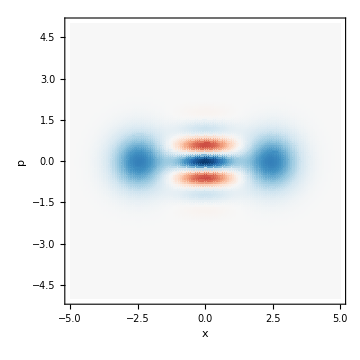
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

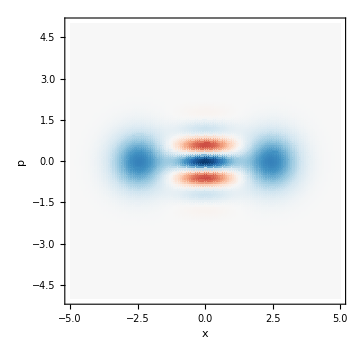
(a) Threshold | (b) Heterodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δx,Δp];
limits=5;
range=60;
α=2;
θ=0;
Δx=Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;

(* Psuccess *)
"Homodyne success probability: "
Re[PsHOM[t,√(1-t^2),α,θ,Δx,ϵHOM[ηH],s]]
"Heterodyne success probability: "
Re[PsHET[t,√(1-t^2),α,θ,Δx,Δp,ϵHET[ηH],s]]


matWnHOM=Table[Re[Chop[WnHOM[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δx,ϵHOM[ηH],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHOM=matWnHOM/(Abs[ Total[matWnHOM,2]](limits/range)^2);

matWnHET=Table[Re[Chop[WnHET[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δx,Δp,ϵHET[ηH],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHET=matWnHET/(Abs[ Total[matWnHET,2]](limits/range)^2);

"Equivalent threshold efficiency for the Homodyne case:"
fitHOM=ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s]
"Equivalent threshold efficiency for the Heterodyne case:"
fitHET=ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]

matWnTHRHOM=Table[Re[Chop[WnTHR[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Re[η/.fitHOM],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnTHRHOM=matWnTHRHOM/(Abs[Total[matWnTHRHOM,2]](limits/range)^2);

matWnTHRHET=Table[Re[Chop[WnTHR[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Re[η/.fitHET],s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnTHRHET=matWnTHRHET/(Abs[Total[matWnTHRHET,2]](limits/range)^2);

"Equivalent Threshold success probability for the Homodyne measurement case: "
PsTHR[t,α,Re[η/.fitHOM],s]
"Equivalent Threshold success probability for the Heterodyne measurement case: "
PsTHR[t,α,Re[η/.fitHET],s]

cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
plotTHRHOM=ListDensityPlot[matWnTHRHOM,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[matWnTHRHOM]],Abs[Min[matWnTHRHOM]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotTHRHET=ListDensityPlot[matWnTHRHET,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[matWnTHRHET]],Abs[Min[matWnTHRHET]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];

plotHOM=ListDensityPlot[matWnHOM,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[matWnHOM]],Abs[Min[matWnHOM]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHET=ListDensityPlot[matWnHET,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[matWnHET]],Abs[Min[matWnHET]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotTHRHOM,plotHOM}}]
Grid[{{"(a) Threshold","(b) Heterodyne"},{plotTHRHET,plotHET}}]
```

```mathematica
(* This ϵ = 2δ = 0 result matches with the ideal homodyne heralding result from Wigner Cat-v2.nb for t=√0.50 *)
```

#### [Obs] Comparing x-Homodyne and Heterodyne measurements

As a function cat state angle θ

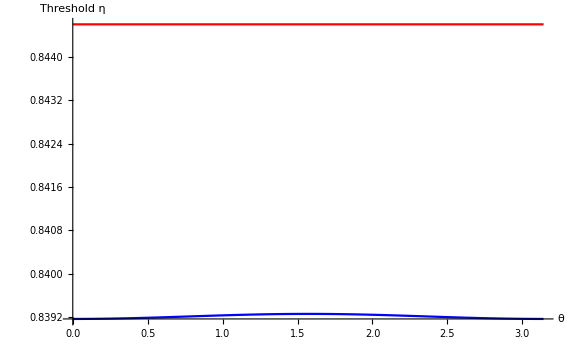

```mathematica
α=2;
Δx=Δp =0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH =0.85; (* dyne efficiency *)
s=1;
ClearAll[θ];
Plot[{η/.ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]},{θ,0,π},AxesLabel->{θ,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* HET gives better efficiency *)
```

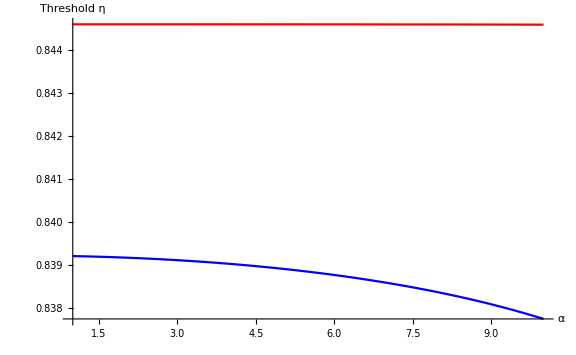

```mathematica
Δx = Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;
θ=0;
ClearAll[α];
Plot[{η/.ηFitHOM[t,r,α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δx,Δp,ϵHET[ηH],s]},{α,1,10},AxesLabel->{α,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* η doesn't seem to depend on α for HET.  *)
```

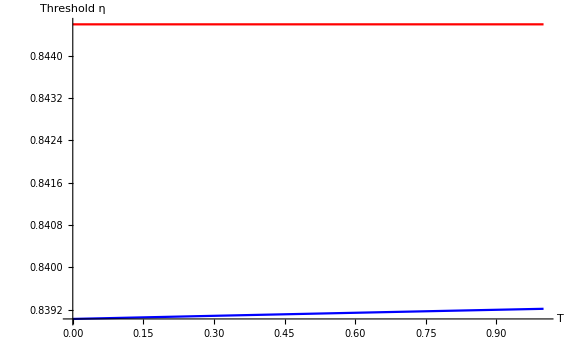

```mathematica
Δx = Δp = 0.3;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH = 0.85; (* dyne efficiency *)
s=1;
α=2;
θ=0;
ClearAll[T];
Plot[{η/.ηFitHOM[√T,√(1-T),α,θ,Δx,ϵHOM[ηH],s],η/.ηFitHET[√T,√(1-T),α,θ,Δx,Δp,ϵHET[ηH],s]},{T,0,1},AxesLabel->{T,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

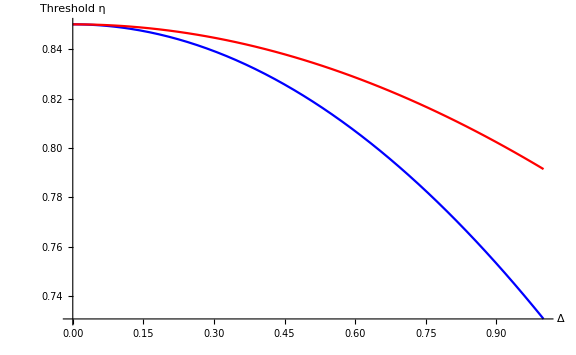

```mathematica
ClearAll[t,r,α,θ,Δ,s];
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
ηH =0.85; (* dyne efficiency *)
s=1;
α=2;
θ=0;

Plot[{η/.ηFitHOM[t,r,α,θ,Δ,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],s]},{Δ,0,1},AxesLabel->{Δ,"Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

```mathematica
(* HET is better for any given Δ *)
```

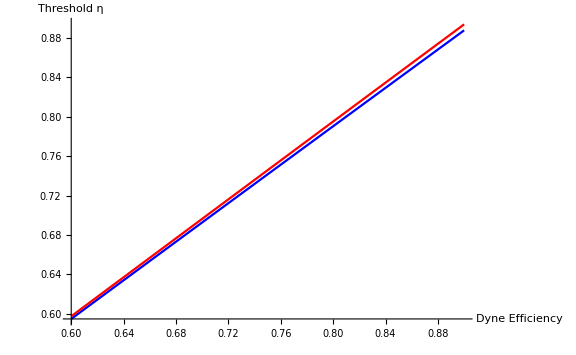

```mathematica
ClearAll[t,r,α,θ,Δ,s,η];
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);
s=1;
α=2;
θ=0;
Δ =0.3;
Plot[{η/.ηFitHOM[t,r,α,θ,Δ,ϵHOM[ηH],s],η/.ηFitHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],s]},{ηH,0.6,0.9},AxesLabel->{"Dyne Efficiency","Threshold η"},PlotStyle->{Blue,Red},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Large]
```

#### [Rslt] When is it definitely better to Heterodyne compared to Thresholding? When the success prob is better.

NEW

Dyne efficiency chosen:

0.85

HOMODYNE:
 
* Equivalence point:

{η→0.733959+0. ⅈ,Δ→0.986858+0. ⅈ}

* RO and RI plots:

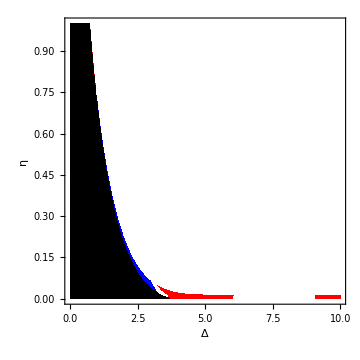

HETERODYNE:
 
* Equivalence point:

FindRoot::jsing: Encountered a singular Jacobian at the point {η,Δ} = {1.96793×10^-10+0. ⅈ,16.4042+0. ⅈ}. Try perturbing the initial point(s).

{η→1.96793×10^-10+0. ⅈ,Δ→16.4042+0. ⅈ}

* RO and RI plots:

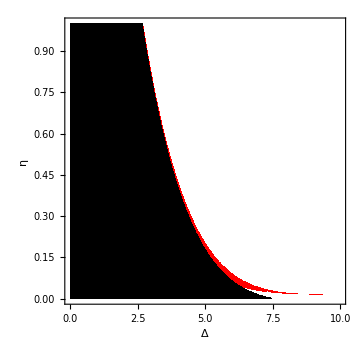

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that heterodyning is better to simulate certain efficiencies. Observation: α needs to be sufficienctly small. But be wary that too small α means we need bigger Δ. *)
ClearAll[α,θ,t,r,s,plotpoints,Δ];
t=√0.75;
r=√(1-t^2);
θ=0;
α=2;
s=1;
"Dyne efficiency chosen:"
ηH =0.85
plotpoints=60;

"HOMODYNE:
 
* Equivalence point:"
EquivalencePointTGTHOM[t,r,α,θ,ϵHOM[ηH],s]
"* RO and RI plots:"
plotROHOM = DensityPlot[HeavisideTheta[Re[FidelityGapHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHOM=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHOM,plotRIHOM}]

"HETERODYNE:
 
* Equivalence point:"
EquivalencePointTGTHET[t,r,α,θ,ϵHET[ηH],s]
"* RO and RI plots:"
plotROHET = DensityPlot[HeavisideTheta[Re[FidelityGapHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHET=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHET,plotRIHET}]

ClearAll[α,θ,t,r,s,plotpoints];
```

OLD

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that heterodyning is better to simulate certain efficiencies. Observation: α needs to be sufficienctly small. But be wary that too small α means we need bigger Δ. *)
ClearAll[α,θ,t,r,s,plotpoints,Δ];
t=√0.75;
r=√(1-t^2);
θ=0;
α=2;
s=1;
"Dyne efficiency chosen:"
ηH =0.85
plotpoints=60;

"HOMODYNE:
 
* Equivalence point:"
EquivalencePointHOM[t,r,α,θ,ϵHOM[ηH],s]
"* RO and RI plots:"
plotROHOM = DensityPlot[HeavisideTheta[Re[ηRelativeOverlapHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHOM=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHOM[t,r,α,θ,Δ,ϵHOM[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHOM,plotRIHOM}]

"HETERODYNE:
 
* Equivalence point:"
EquivalencePointHET[t,r,α,θ,ϵHET[ηH],s]
"* RO and RI plots:"
plotROHET = DensityPlot[HeavisideTheta[Re[ηRelativeOverlapHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRIHET=DensityPlot[HeavisideTheta[Re[PsηRelativeImprovementHET[t,r,α,θ,Δ,Δ,ϵHET[ηH],η,s]]],{Δ,0,10},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotROHET,plotRIHET}]

ClearAll[α,θ,t,r,s,plotpoints];
```

Dyne efficiency chosen:

0.85

HOMODYNE:
 
* Equivalence point:

{η→0.733959+0. ⅈ,Δ→0.986858+0. ⅈ}

* RO and RI plots:

-Graphics-

HETERODYNE:
 
* Equivalence point:

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{η→1.50573×10^-9+0. ⅈ,Δ→15.6925+0. ⅈ}

* RO and RI plots:

-Graphics-

#### [Obs]

HET doesn’t seem to depend on α very strongly or beam splitter transmittance T which is strange. Its independence from θ makes sense though as we measure both x and p.
“Equivalence point” which is where the success prob of threshold is equal to success prob of dyneing occurs close to zero efficiency --- numerically. 
This means whenever we have sufficiently efficient threshold detectors available, we should prefer those. 
However, the situation much more interesting in the Homodyne case.